```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/nathan/olin/fall2016/ThinkBayes2/bayesianLinearRegression

```mathematica
intensityData=Import["intensityData.csv","CSV"];
monthHeightData=Import["monthsHeights.csv","CSV"];
fittedLine=Import["fittedLineCSV.csv","CSV"];
```

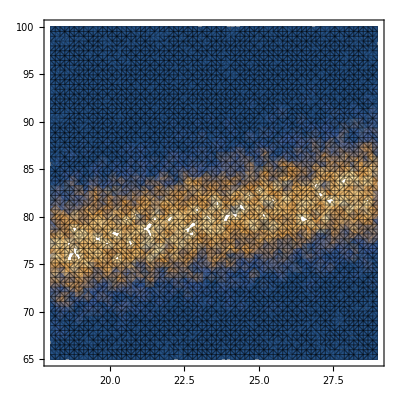

```mathematica
densityPlot=ListDensityPlot[intensityData,Mesh->All]
```

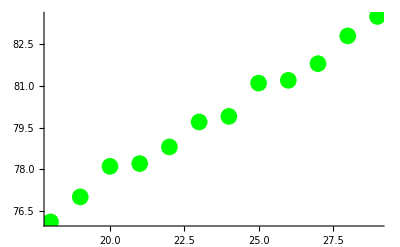

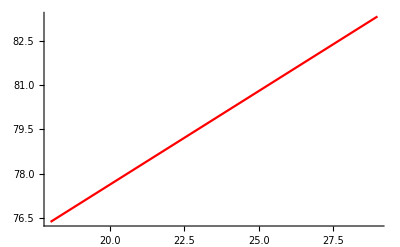

```mathematica
dataPlot=ListPlot[monthHeightData,PlotStyle->Directive[Green,PointSize[.03]]]
fittedLinePlot=ListLinePlot[fittedLine,PlotStyle->Red]
```

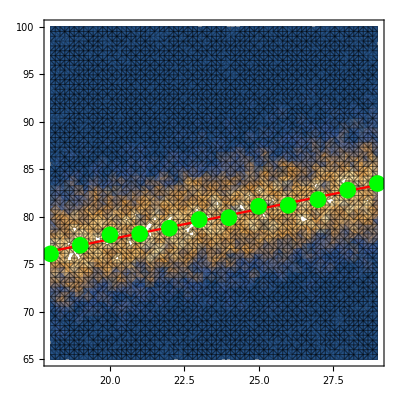

```mathematica
Show[densityPlot,dataPlot,fittedLinePlot]
```

```mathematica
Export["ageHeightAllPlots3.png",%]
```

ageHeightAllPlots3.png